# 7 - answers to challenges

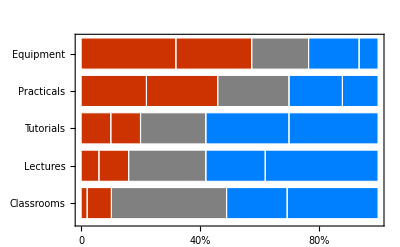

```mathematica
(* Challenge 1 *)

scores = {"Bad", "Not good", "OK", "Good", "Excellent"};
areas = {"Classrooms", "Lectures", "Tutorials", "Practicals",
         "Equipment"};
data = {{1, 4, 19, 10, 15},
        {3, 5, 13, 10, 19},
        {5, 5, 11, 14, 15},
        {11, 12, 12, 9, 6},
        {15, 12, 9, 8, 3}};

badColour = Directive[EdgeForm[{RGBColor[1,1,1,1],Thick}],RGBColor[0.8,0.2,0]];
goodColour = Directive[EdgeForm[{RGBColor[1,1,1,1],Thick}],RGBColor[0,.5,1]];
neutralColour = Directive[EdgeForm[{RGBColor[1,1,1,1],Thick}],GrayLevel[0.5]];

BarChart[data,
	ChartLayout->"Percentile",
	BarOrigin->Left,
	BarSpacing->{0.2},
	Frame->{True,True,False,False},
	FrameStyle->{RGBColor[1,1,1,0],Automatic},
	FrameTicks->{{0, {20, "20%"}, {40, "40%"}, {60, "60%"}, {80, "80%"}, {100,"100%"}},
	             Automatic},
	ChartLabels->{Map[Style[#,RGBColor[.4,.4,.4,1]]&, areas], None},
	ChartStyle->{badColour, badColour, neutralColour,
	            goodColour, goodColour},
	PlotLabel->Style["\n",18],
	
	Epilog->{
		Style[Text["How do you evaluate this course?",
		           {-25, 6}, {-1,-1}],
		      FontSize->14, GrayLevel[0.2]],
		Text[Row[{
		        Style["Bad", badColour], "   ", 
		        Style["Not good", badColour], "   ",
		        Style["OK", neutralColour], "   ",
		        Style["Good", goodColour], "   ",
		        Style["Excellent", goodColour]
		     }], {0, 5.6}, {-1,-1}]
	}
]
```

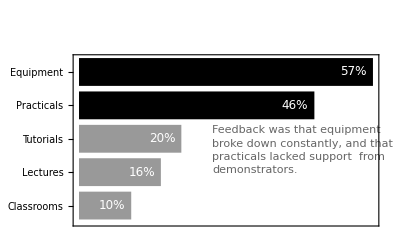

```mathematica
(* Challenge 2 *)

genLines[lines_, startPt_, spacing_, offset_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, offset],
		  opts], {n, 0, Length[lines]-1}]

text = {
	Row[{"Feedback was that ", Style["equipment", Black, Bold]}],
	Row[{Style["broke down", Black, Bold], " constantly, and that"}],
	Row[{Style["practicals lacked support ",Bold,Black], " from"}],
	"demonstrators."
};

bgColour = RGBColor[0.6,0.6,0.6,1];
hlColour = Black;

areas = {"Classrooms", "Lectures", "Tutorials", Style["Practicals", hlColour],
         Style["Equipment", hlColour]};
data = {{1, 4, 19, 10, 15},
        {3, 5, 13, 10, 19},
        {5, 5, 11, 14, 15},
        {11, 12, 12, 9, 6},
        {15, 12, 9, 8, 3}};

badFracs = Map[100(#⟦1⟧+#⟦2⟧)/Total[#]&, data];
badFracs⟦4⟧ = Style[badFracs⟦4⟧, Black];
badFracs⟦5⟧ = Style[badFracs⟦5⟧, Black];

BarChart[badFracs,
	ChartLabels->Map[Style[#,bgColour,12]&, areas],
	BarOrigin->Left,
	BarSpacing->0.2,
	Frame->{True,True,False,False},
	FrameStyle->RGBColor[1,1,1,0],
	FrameTicks->{None, Automatic},
	ChartStyle->Directive[EdgeForm[None], bgColour],
	LabelingFunction->(Placed[Style[Row[{Round[#], "%"}],FontSize->12, White],
	                         Right]&),
	PlotLabel->Style["\n", 18],
	
	Epilog->{
		Style[Text["We need better equipment and practicals",
		           {-14,6.5}, {-1,-1}],
		      FontSize->16, GrayLevel[0.2]],
		Style[Text["Proportion of students who thought the the course's equipment and",
		           {-14,6.1}, {-1,-1}],
		      FontSize->11, GrayLevel[0.5]],
		Style[Text[Row[{"practicals were ", Style["not good", Black,Bold], " or ", Style["bad.", Black,Bold]}],
		           {-14,5.7}, {-1,-1}],
		      FontSize->11, GrayLevel[0.5]],
		
		GrayLevel[0.4],
		genLines[text, {26,3.4}, 0.4, {-1,1}, FontSize->11]
	}
]
```